# Morgan Nance Mathematica Exam Section A

```mathematica
a = List[1, Pi, 0.37, E^6 ];
```

```mathematica
b = a + 2 //N
```

{3.,5.14159,2.37,405.429}

```mathematica
c = List[9^17, Cos[13], Log[7], Factorial[7]];
```

```mathematica
c/2//N
```

{8.33859×10^15,0.453723,0.972955,2520.}

```mathematica
d =Range[0,6,0.1];
```

```mathematica
Length[d]
```

61

```mathematica
myprimes=Table[Prime[ii],{ii,1,20}]
Export["/Users/mlnance/Desktop/myprimes.txt",myprimes]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71}

/Users/mlnance/Desktop/myprimes.txt

```mathematica
randomnumbers=Import["/Users/mlnance/Desktop/randomnumbers.txt","Data"];
```

```mathematica
Mean[randomnumbers[[;;10]]]
Mean[randomnumbers[[;;100]]]
Mean[randomnumbers[[;;300]]]
Mean[randomnumbers[[;;1000]]]
```

{2.16801}

{2.14317}

{2.14455}

{2.11627}

```mathematica
StandardDeviation[randomnumbers[[;;10]]]
StandardDeviation[randomnumbers[[;;100]]]
StandardDeviation[randomnumbers[[;;300]]]
StandardDeviation[randomnumbers[[;;1000]]]
```

{0.474534}

{0.492523}

{0.480228}

{0.496242}

```mathematica
Total[Table[(Mean[randomnumbers[[;;10]]]-randomnumbers[[ii]])^2,{ii,1,10}]]/9
Variance[randomnumbers[[;;10]]]
StandardDeviation[randomnumbers[[;;10]]]^2
```

{0.225182}

{0.225182}

{0.225182}

```mathematica
Section B
```

```mathematica
myprimesagain=Transpose[Import["/Users/mlnance/Desktop/myprimes.txt","Data"]]
```

{{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71}}

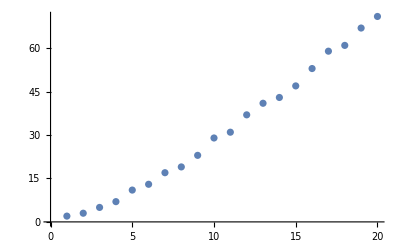

```mathematica
ListPlot[myprimesagain]
```

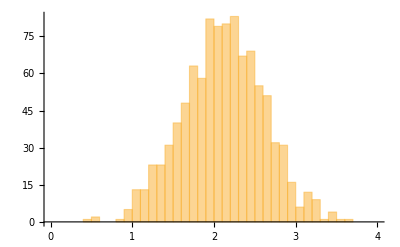

```mathematica
randomnumbers=Transpose[Import["/Users/mlnance/Desktop/randomnumbers.txt","Data"]];
Histogram[randomnumbers,{0.1},PlotRange->{{0,4},Automatic}](*Gaussian Distribution?*)
```

```mathematica
(*I don't understand B3*)
```

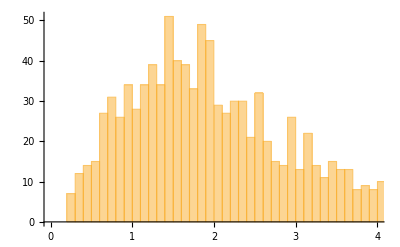

```mathematica
otherrandomnumbers=Transpose[Import["/Users/mlnance/Desktop/otherrandomnumbers.txt","Data"]];
Histogram[otherrandomnumbers,{0.1},PlotRange->{{0,4},Automatic}]
(*I don't know what distribution this would be*)
```

```mathematica
yn[an_,bn_,xn_]:=an+bn*xn
yd[ad_,bd_,xd_]:=ad+bd*xd
dg[dgh2o_,m_,x_]:=dgh2o+m*x
k[dgh2o_,m_,x_,t_]:=Exp[-dg[dgh2o,m,x]/(8.314*t)]
```